## Linear Coverage

```mathematica
Clear["Global`*"]
c[q_,e_]:=(q/N)*e
d[p_,q_,e_]:=m*((1-θ)-p+θ*c[q,e])
Π[p_,q_,e_]:=p*q -γ*q-δ*e^2
Α[p_,q_,e_]:=p*q -(p+α)*(q-d[p,q,e])-γ*q-δ*e^2
```

```mathematica
Simplify[Α[p,N,(N *(α+γ))/(m (p+α) θ)]]
Simplify[Α[p,N,(m (p+α) θ)/(2 δ)]]
```

N p-N γ-(N^2 (α+γ)^2 δ)/(m^2 (p+α)^2 θ^2)-(p+α) ((N (p-γ))/(p+α)+m (-1+p+θ))

-N (α+γ)+(m^2 (p+α)^2 θ^2)/(4 δ)-m (p+α) (-1+p+θ)

```mathematica
Simplify[Α[p,(m (p+α) (1-p-θ))/(p-γ),(N *(α+γ))/(m (p+α) θ)]]
Simplify[Α[p,(m *N* (-1+p+θ))/(-N+b m θ),b]] (* b = eFOC*)
```

-(N^2 (α+γ)^2 δ)/(m^2 (p+α)^2 θ^2)-m (p+α) (-1+p+θ)

(-b^2 N δ+b^3 m δ θ-m N (p-γ) (-1+p+θ))/(N-b m θ)

```mathematica
(* FOC of the cubic *)
(* Solve[-(2 e N^2 δ-4 e^2 m N δ θ+2 e^3 m^2 δ θ^2+m^2 N* (p-γ)* θ* (-1+p+θ))==0,e]*)
Subscript[e, FOC]=(2 N)/(3 m θ)-(2 2^(1/3) N^2 δ)/(3 (16 m^3 N^3 δ^3 θ^3-108 m^6 N p δ^2 θ^5+108 m^6 N p^2 δ^2 θ^5+108 m^6 N γ δ^2 θ^5-108 m^6 N p γ δ^2 θ^5+108 m^6 N p δ^2 θ^6-108 m^6 N γ δ^2 θ^6+√(-256 m^6 N^6 δ^6 θ^6+(16 m^3 N^3 δ^3 θ^3-108 m^6 N p δ^2 θ^5+108 m^6 N p^2 δ^2 θ^5+108 m^6 N γ δ^2 θ^5-108 m^6 N p γ δ^2 θ^5+108 m^6 N p δ^2 θ^6-108 m^6 N γ δ^2 θ^6)^2))^(1/3))-1/(6 2^(1/3) m^2 δ θ^2)(16 m^3 N^3 δ^3 θ^3-108 m^6 N p δ^2 θ^5+108 m^6 N p^2 δ^2 θ^5+108 m^6 N γ δ^2 θ^5-108 m^6 N p γ δ^2 θ^5+108 m^6 N p δ^2 θ^6-108 m^6 N γ δ^2 θ^6+√(-256 m^6 N^6 δ^6 θ^6+(16 m^3 N^3 δ^3 θ^3-108 m^6 N p δ^2 θ^5+108 m^6 N p^2 δ^2 θ^5+108 m^6 N γ δ^2 θ^5-108 m^6 N p γ δ^2 θ^5+108 m^6 N p δ^2 θ^6-108 m^6 N γ δ^2 θ^6)^2))^(1/3)
```

(2 N)/(3 m θ)-(2 2^(1/3) N^2 δ)/(3 (16 m^3 N^3 δ^3 θ^3-108 m^6 N p δ^2 θ^5+108 m^6 N p^2 δ^2 θ^5+108 m^6 N γ δ^2 θ^5-108 m^6 N p γ δ^2 θ^5+108 m^6 N p δ^2 θ^6-108 m^6 N γ δ^2 θ^6+√(-256 m^6 N^6 δ^6 θ^6+(16 m^3 N^3 δ^3 θ^3-108 m^6 N p δ^2 θ^5+108 m^6 N p^2 δ^2 θ^5+108 m^6 N γ δ^2 θ^5-108 m^6 N p γ δ^2 θ^5+108 m^6 N p δ^2 θ^6-108 m^6 N γ δ^2 θ^6)^2))^(1/3))-1/(6 2^(1/3) m^2 δ θ^2)(16 m^3 N^3 δ^3 θ^3-108 m^6 N p δ^2 θ^5+108 m^6 N p^2 δ^2 θ^5+108 m^6 N γ δ^2 θ^5-108 m^6 N p γ δ^2 θ^5+108 m^6 N p δ^2 θ^6-108 m^6 N γ δ^2 θ^6+√(-256 m^6 N^6 δ^6 θ^6+(16 m^3 N^3 δ^3 θ^3-108 m^6 N p δ^2 θ^5+108 m^6 N p^2 δ^2 θ^5+108 m^6 N γ δ^2 θ^5-108 m^6 N p γ δ^2 θ^5+108 m^6 N p δ^2 θ^6-108 m^6 N γ δ^2 θ^6)^2))^(1/3)

### Second Case Comparison

```mathematica
Simplify[Α[p,N,(m* (p+α) θ)/(2 δ)]]
Simplify[Α[p,(m (p+α) (1-p-θ))/(p-γ),(N *(α+γ))/(m *(p+α) θ)]]
```

-N (α+γ)+(m^2 (p+α)^2 θ^2)/(4 δ)-m (p+α) (-1+p+θ)

-(N^2 (α+γ)^2 δ)/(m^2 (p+α)^2 θ^2)-m (p+α) (-1+p+θ)

```mathematica
Reduce[-(N^2 (α+γ)^2 δ)/(m^2 (p+α)^2 θ^2) - (-N (α+γ)+(m^2 (p+α)^2 θ^2)/(4 δ)) ≥  0&&0<p≤1&&0≤α≤1&& (N *(α+γ))/(m (p+α))<θ≤1&&0<γ≤1 && 0<m<N&&N>0 && p>γ&&1-p-θ>0&&0<δ≤ (m^3 (p+α)^3 θ^2 (1-p-θ))/(2*N^2 (p-γ) (α+γ)),δ]
```

False

### First Case Comparison:δ > (m^2*(p+α)^2*θ^2)/(2*N*(α+γ))

```mathematica
Simplify[Solve[D[Simplify[Α[p,q,e]],e] ==0,e]]
Z[q_]:=(m *q*(p+α)*θ)/(2 *N *δ)
Simplify[Z[(m *N* (-1+p+θ))/(-N+b* m* θ)]]
```

{{e→(m q (p+α) θ)/(2 N δ)}}

-(m^2 (p+α) θ (-1+p+θ))/(2 δ (N-b m θ))

```mathematica
Simplify[-(m^2 (p+α) θ (-1+p+θ))/(2 (m^2*(p+α)^2*θ^2)/(2*N*(α+γ))(N-b m θ))]
```

(N (α+γ) (-1+p+θ))/((p+α) θ (-N+b m θ))

### Third Case Comparison:...<δ ≤ (m^2*(p+α)^2*θ^2)/(2*N*(α+γ))

```mathematica
Simplify[Α[p,N,(m (p+α) θ)/(2 δ)]]
Simplify[Α[p,(m *N* (-1+p+θ))/(-N+b m θ),b]]
```

-N (α+γ)+(m^2 (p+α)^2 θ^2)/(4 δ)-m (p+α) (-1+p+θ)

(-b^2 N δ+b^3 m δ θ-m N (p-γ) (-1+p+θ))/(N-b m θ)

```mathematica
(* Simplify[Reduce[ -N (α+γ)+(m^2 (p+α)^2 θ^2)/(4 δ)-m (p+α) (-1+p+θ)-((-b^2 N δ+b^3 m δ θ-m N (p-γ) (-1+p+θ))/(N-b m θ))≥0&&q≤N&&0<p≤1&&0≤α≤1&& (N *(α+γ))/(m (p+α))<θ≤1&&0<γ≤1&& 0<e≤1 && 0<m<N&&N>0 && p>γ&&1-p-θ>0 && δ≥ (m^3 (p+α)^3 θ^2 (1-p-θ))/(2*N^2 (p-γ) (α+γ)),δ,Reals,Backsubstitution->True]]*)
```

## Linear Search Cost

```mathematica
Clear["Global`*"]
d[p_,q_,e_]:=m*(1-(θ+p-Subscript[β, 1]*q-Subscript[β, 2]*e))
Π[p_,q_,e_]:=p*q -γ*q-δ*e^2
Α[p_,q_,e_]:=p*q -(p+α)*(q-d[p,q,e])-γ*q-δ*e^2
```

```mathematica
Simplify[D[Α[p,q,e],q]]
Simplify[D[Α[p,q,e],e]]
Simplify[D[D[Α[p,q,e],q],q]]
Simplify[D[D[Α[p,q,e],e],e]]
```

-α-γ+m (p+α) β_1

-2 e δ+m (p+α) β_2

0

-2 δ

### Left endpoint

```mathematica
Simplify[Solve[q==d[p,q,e] &&D[Α[p,q,e],e]==0 ,{q,e}]]
```

{{q→-(m (-2 δ (-1+p+θ)+m (p+α) β_2^2))/(2 δ (-1+m β_1)),e→(m (p+α) β_2)/(2 δ)}}

### Right endpoint

```mathematica
Simplify[Solve[Subscript[β, 1]*q+Subscript[β, 2]*e==θ+p&&D[Α[p,q,e],e]==0,{q,e}]]
```

{{q→(2 δ (p+θ)-m (p+α) β_2^2)/(2 δ β_1),e→(m (p+α) β_2)/(2 δ)}}

#### Left less than right

```mathematica
Reduce[-(m (-2 δ (-1+p+θ)+m (p+α) Subscript[β, 2]^2))/(2 δ (-1+m Subscript[β, 1]))≤ (2 δ (p+θ)-m (p+α) Subscript[β, 2]^2)/(2 δ Subscript[β, 1])&&p>γ&&0<p<1&& γ >0&&m>0&&0<Subscript[β, 1]<γ/(m p)&&0<Subscript[β, 2]&&α>0,α]
```

0<γ<1&&γ<p<1&&β_1>0&&0<m<γ/(p β_1)&&β_2>0&&((δ<0&&((θ<(-2 p δ+2 m δ β_1+m p β_2^2)/(2 δ)&&α≥(2 p δ+2 δ θ-2 m δ β_1-m p β_2^2)/(m β_2^2))||(θ==(-2 p δ+2 m δ β_1+m p β_2^2)/(2 δ)&&α>(2 p δ+2 δ θ-2 m δ β_1-m p β_2^2)/(m β_2^2))||(θ>(-2 p δ+2 m δ β_1+m p β_2^2)/(2 δ)&&α>0)))||(δ>0&&θ>(-2 p δ+2 m δ β_1+m p β_2^2)/(2 δ)&&0<α≤(2 p δ+2 δ θ-2 m δ β_1-m p β_2^2)/(m β_2^2)))

### Optimal condition for β and α

```mathematica
Reduce[(γ+α)/(m*(α+p))< Subscript[β, 1]&& p>γ&&0<p<1&& γ >0&&m>0&&α>0,α]
```

0<γ<1&&γ<p<1&&m>0&&((γ/(m p)<β_1<1/m&&0<α<(γ-m p β_1)/(-1+m β_1))||(β_1≥1/m&&α>0))

### Compute Π_1 and Π_2

```mathematica
Simplify[Solve[q==d[p,q,0],q]]
Simplify[Solve[q==d[p,q,(m (p+α) Subscript[β, 2])/(2 δ)],q]]
```

{{q→(m (-1+p+θ))/(-1+m β_1)}}

{{q→-(m (-2 δ (-1+p+θ)+m (p+α) β_2^2))/(2 δ (-1+m β_1))}}

```mathematica
Simplify[Π[p,(m (-1+p+θ))/(-1+m Subscript[β, 1]),0]]
Simplify[Α[p,-(m (-2 δ (-1+p+θ)+m (p+α) Subscript[β, 2]^2))/(2 δ (-1+m Subscript[β, 1])),(m (p+α) Subscript[β, 2])/(2 δ)]]
Simplify[Α[p,(2 δ (p+θ)-m (p+α) Subscript[β, 2]^2)/(2 δ Subscript[β, 1]),(m (p+α) Subscript[β, 2])/(2 δ)]]
```

(m (p-γ) (-1+p+θ))/(-1+m β_1)

-(m (-4 (p-γ) δ (-1+p+θ)+m (p+α) (p-α-2 γ+m (p+α) β_1) β_2^2))/(4 δ (-1+m β_1))

(-m (p+α) β_1 (-4 δ+m (p+α) β_2^2)+2 (α+γ) (-2 δ (p+θ)+m (p+α) β_2^2))/(4 δ β_1)

### Compare for global optimal

#### First case

```mathematica
Simplify[Π[p,(m (-1+p+θ))/(-1+m Subscript[β, 1]),0] -Α[p,-(m (-2 δ (-1+p+θ)+m (p+α) Subscript[β, 2]^2))/(2 δ (-1+m Subscript[β, 1])),(m (p+α) Subscript[β, 2])/(2 δ)]]
Reduce[p-α-2 γ+m (p+α) Subscript[β, 1]≤ 0 &&0<Subscript[β, 1]<γ/(m p)&&p>γ&&0<p<1&& γ >0&&m>0]
```

(m^2 (p+α) (p-α-2 γ+m (p+α) β_1) β_2^2)/(4 δ (-1+m β_1))

0<γ<1&&γ<p<1&&β_1>0&&0<m<γ/(p β_1)&&α≥(-p+2 γ-m p β_1)/(-1+m β_1)

#### Second case

```mathematica
Simplify[Π[p,(m (-1+p+θ))/(-1+m Subscript[β, 1]),0] -Α[p,-(m (-2 δ (-1+p+θ)+m (p+α) Subscript[β, 2]^2))/(2 δ (-1+m Subscript[β, 1])),(m (p+α) Subscript[β, 2])/(2 δ)]]
Reduce[p-α-2 γ+m (p+α) Subscript[β, 1]≤ 0 &&γ/(m p)<Subscript[β, 1]<1/m&&p>γ&&0<p<1&& γ >0&&m>0&&α>(γ-m p Subscript[β, 1])/(-1+m Subscript[β, 1]),α]
```

(m^2 (p+α) (p-α-2 γ+m (p+α) β_1) β_2^2)/(4 δ (-1+m β_1))

0<γ<1&&γ<p<1&&m>0&&γ/(m p)<β_1<1/m&&α≥(-p+2 γ-m p β_1)/(-1+m β_1)

#### Third case

```mathematica
Simplify[Π[p,(m (-1+p+θ))/(-1+m Subscript[β, 1]),0] -Α[p,(2 δ (p+θ)-m (p+α) Subscript[β, 2]^2)/(2 δ Subscript[β, 1]),(m (p+α) Subscript[β, 2])/(2 δ)]]
Reduce[m^2 (p+α) Subscript[β, 1]^2 (-4 δ+m (p+α) Subscript[β, 2]^2)+2 (α+γ) (-2 δ (p+θ)+m (p+α) Subscript[β, 2]^2)+m Subscript[β, 1] (4 δ (p^2+α+γ+α θ+p (α+θ))-m (p+α) (p+3 α+2 γ) Subscript[β, 2]^2)≤ 0&&γ/(m p)<Subscript[β, 1]<1/m&&p>γ&&0<p<1&& γ >0&&m>0&&0<Subscript[β, 2]<1&&θ+p <1&&δ>0&&0<α<(γ-m p Subscript[β, 1])/(-1+m Subscript[β, 1]),δ]
```

(m^2 (p+α) β_1^2 (-4 δ+m (p+α) β_2^2)+2 (α+γ) (-2 δ (p+θ)+m (p+α) β_2^2)+m β_1 (4 δ (p^2+α+γ+α θ+p (α+θ))-m (p+α) (p+3 α+2 γ) β_2^2))/(4 δ β_1 (-1+m β_1))

$Aborted

```mathematica
Y[α_]:=m^2 (p+α) Subscript[β, 1]^2 (-4 δ+m (p+α) Subscript[β, 2]^2)+2 (α+γ) (-2 δ (p+θ)+m (p+α) Subscript[β, 2]^2)+m Subscript[β, 1] (4 δ (p^2+α+γ+α θ+p (α+θ))-m (p+α) (p+3 α+2 γ) Subscript[β, 2]^2)
Simplify[Y[0]]
Simplify[Y[(γ-m p Subscript[β, 1])/(-1+m Subscript[β, 1])]]
```

m^2 p β_1^2 (-4 δ+m p β_2^2)+2 γ (-2 δ (p+θ)+m p β_2^2)+m β_1 (4 δ (p^2+γ+p θ)-m p (p+2 γ) β_2^2)

-(m^2 (p-γ)^2 β_1 β_2^2)/(-1+m β_1)

```mathematica
Simplify[D[Y[α],α]]
Simplify[D[Simplify[D[Y[α],α]],α]] (* The difference between is a convex function *)
```

2 (-1+m β_1) (2 δ (p+θ)-m (p+2 α+γ) β_2^2+m β_1 (-2 δ+m (p+α) β_2^2))

2 m (-2+m β_1) (-1+m β_1) β_2^2

```mathematica
Z[α_]:=(-m (p+α) Subscript[β, 1] (-4 δ+m (p+α) Subscript[β, 2]^2)+2 (α+γ) (-2 δ (p+θ)+m (p+α) Subscript[β, 2]^2))/(4 δ Subscript[β, 1])
Simplify[Solve[Simplify[D[Z[α],α]]==0,α]]
Simplify[Z[0]]
Simplify[Z[(γ-m p Subscript[β, 1])/(-1+m Subscript[β, 1])]]
```

{{α→(-2 δ (p+θ)+m (p+γ) β_2^2+m β_1 (2 δ-m p β_2^2))/(m (-2+m β_1) β_2^2)}}

(-4 γ δ (p+θ)+2 m p γ β_2^2+m p β_1 (4 δ-m p β_2^2))/(4 δ β_1)

(m (p-γ) (-4 δ (-1+p+θ)+4 m δ (-1+p+θ) β_1+m (p-γ) β_2^2))/(4 δ (-1+m β_1)^2)

#### Left/Right endpoint - demand

```mathematica
Simplify[-(m (-2 δ (-1+p+θ)+m (p+α) Subscript[β, 2]^2))/(2 δ (-1+m Subscript[β, 1]))-d[p,-(m (-2 δ (-1+p+θ)+m (p+α) Subscript[β, 2]^2))/(2 δ (-1+m Subscript[β, 1])),(m (p+α) Subscript[β, 2])/(2 δ)]]
Simplify[(2 δ (p+θ)-m (p+α) Subscript[β, 2]^2)/(2 δ Subscript[β, 1])-d[p,(2 δ (p+θ)-m (p+α) Subscript[β, 2]^2)/(2 δ Subscript[β, 1]),(m (p+α) Subscript[β, 2])/(2 δ)]]
```

0

-m+(2 δ (p+θ)-m (p+α) β_2^2)/(2 δ β_1)

### Plot profit function

```mathematica
Simplify[Π[p,(m (-1+p+θ))/(-1+m Subscript[β, 1]),0]]
Simplify[Α[p,-(m (-2 δ (-1+p+θ)+m (p+α) Subscript[β, 2]^2))/(2 δ (-1+m Subscript[β, 1])),(m (p+α) Subscript[β, 2])/(2 δ)]]
Simplify[Α[p,(2 δ (p+θ)-m (p+α) Subscript[β, 2]^2)/(2 δ Subscript[β, 1]),(m (p+α) Subscript[β, 2])/(2 δ)]]
```

(m (p-γ) (-1+p+θ))/(-1+m β_1)

-(m (-4 (p-γ) δ (-1+p+θ)+m (p+α) (p-α-2 γ+m (p+α) β_1) β_2^2))/(4 δ (-1+m β_1))

(-m (p+α) β_1 (-4 δ+m (p+α) β_2^2)+2 (α+γ) (-2 δ (p+θ)+m (p+α) β_2^2))/(4 δ β_1)

#### When 0<β_1<γ/(m p), plot Π_1 and Π_2

{0.3,100,0.05,0.05,100,0.00133333,0.2}

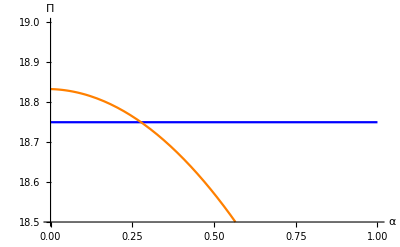

```mathematica
{p=0.3,m=100,θ=0.05,γ=0.05,δ=100,Subscript[β, 1]=0.4/300,Subscript[β, 2]=0.2}
Show[{Plot[(m (p-γ) (-1+p+θ))/(-1+m Subscript[β, 1]),{α,0,1},PlotStyle->Blue,PlotRange->{18.5,19}],Plot[-(m (-4 (p-γ) δ (-1+p+θ)+m (p+α) (p-α-2 γ+m (p+α) Subscript[β, 1]) Subscript[β, 2]^2))/(4 δ (-1+m Subscript[β, 1])),{α,0,1},PlotStyle->Orange,PlotRange->{18.5,19}]},PlotRange->{18.5,19},AxesLabel->{α,Π}]
```

#### Corresponding q, e

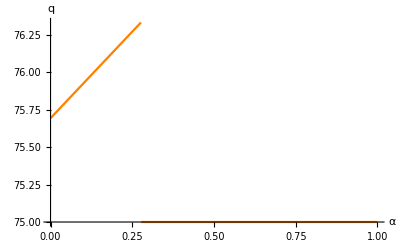

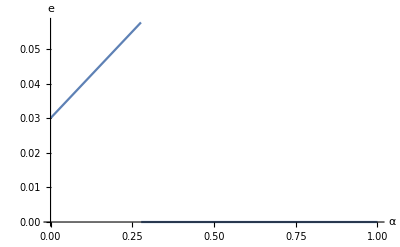

```mathematica
Plot[Piecewise[{{-(m (-2 δ (-1+p+θ)+m (p+α) Subscript[β, 2]^2))/(2 δ (-1+m Subscript[β, 1])),α<(-p+2 γ-m p Subscript[β, 1])/(-1+m Subscript[β, 1])},{(m (-1+p+θ))/(-1+m Subscript[β, 1]),(-p+2 γ-m p Subscript[β, 1])/(-1+m Subscript[β, 1])<α}}],{α,0,1},PlotStyle->Orange,PlotRange->Automatic,AxesLabel->{α,q}]
Plot[Piecewise[{{(m (p+α) Subscript[β, 2])/(2 δ),α<(-p+2 γ-m p Subscript[β, 1])/(-1+m Subscript[β, 1])},{0,(-p+2 γ-m p Subscript[β, 1])/(-1+m Subscript[β, 1])<α}}],{α,0,1},AxesLabel->{α,e}]
```

#### When γ/(m p)<β_1<1/m, plot Π_1 and Π_2and the corresponding q, e

{0.3,100,0.05,0.05,100,1/300,0.2}

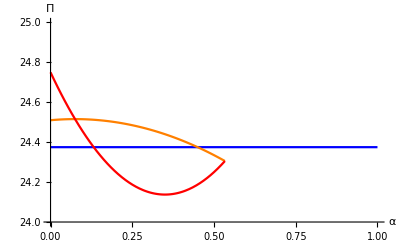

```mathematica
{p=0.3,m=100,θ=0.05,γ=0.05,δ=100,Subscript[β, 1]=1/300,Subscript[β, 2]=0.2}
Show[{Plot[(m (p-γ) (-1+p+θ))/(-1+m Subscript[β, 1]),{α,0,1},PlotStyle->Blue,PlotRange->{24,25}],Plot[-(m (-4 (p-γ) δ (-1+p+θ)+m (p+α) (p-α-2 γ+m (p+α) Subscript[β, 1]) Subscript[β, 2]^2))/(4 δ (-1+m Subscript[β, 1])),{α,0,(2 p δ+2 δ θ-2 m δ Subscript[β, 1]-m p Subscript[β, 2]^2)/(m Subscript[β, 2]^2)},PlotStyle->Orange,PlotRange->{24,25}],
Plot[(-m (p+α) Subscript[β, 1] (-4 δ+m (p+α) Subscript[β, 2]^2)+2 (α+γ) (-2 δ (p+θ)+m (p+α) Subscript[β, 2]^2))/(4 δ Subscript[β, 1]),{α,0,(2 p δ+2 δ θ-2 m δ Subscript[β, 1]-m p Subscript[β, 2]^2)/(m Subscript[β, 2]^2)},PlotStyle->Red,PlotRange->{24,25}]},PlotRange->{24,25},AxesLabel->{α,Π}]
```

#### Corresponding q, e

```mathematica
Solve[(-m (p+α) Subscript[β, 1] (-4 δ+m (p+α) Subscript[β, 2]^2)+2 (α+γ) (-2 δ (p+θ)+m (p+α) Subscript[β, 2]^2))/(4 δ Subscript[β, 1])==-(m (-4 (p-γ) δ (-1+p+θ)+m (p+α) (p-α-2 γ+m (p+α) Subscript[β, 1]) Subscript[β, 2]^2))/(4 δ (-1+m Subscript[β, 1])),α]
```

{{α→0.075},{α→0.533333}}

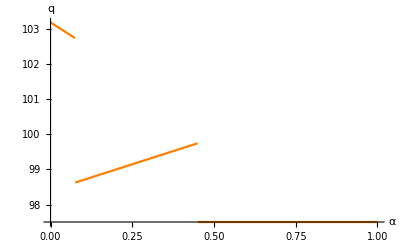

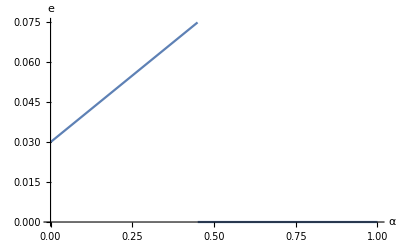

```mathematica
Plot[Piecewise[{{(2 δ (p+θ)-m (p+α) Subscript[β, 2]^2)/(2 δ Subscript[β, 1]),α≤ 0.07499},{-(m (-2 δ (-1+p+θ)+m (p+α) Subscript[β, 2]^2))/(2 δ (-1+m Subscript[β, 1])),0.07499<α<(-p+2 γ-m p Subscript[β, 1])/(-1+m Subscript[β, 1])},{(m (-1+p+θ))/(-1+m Subscript[β, 1]),(-p+2 γ-m p Subscript[β, 1])/(-1+m Subscript[β, 1])<α}}],{α,0,1},PlotStyle->Orange,PlotRange->Automatic,AxesLabel->{α,q}]
Plot[Piecewise[{{(m (p+α) Subscript[β, 2])/(2 δ),α<(-p+2 γ-m p Subscript[β, 1])/(-1+m Subscript[β, 1])},{0,(-p+2 γ-m p Subscript[β, 1])/(-1+m Subscript[β, 1])<α}}],{α,0,1},AxesLabel->{α,e}]
```

#### To derive the third case α, find the intersection of two Π_2

```mathematica
Solve[-(m (-4 (p-γ) δ (-1+p+θ)+m (p+α) (p-α-2 γ+m (p+α) Subscript[β, 1]) Subscript[β, 2]^2))/(4 δ (-1+m Subscript[β, 1]))==(-m (p+α) Subscript[β, 1] (-4 δ+m (p+α) Subscript[β, 2]^2)+2 (α+γ) (-2 δ (p+θ)+m (p+α) Subscript[β, 2]^2))/(4 δ Subscript[β, 1]),α]
```

{{α→(γ-m p β_1)/(-1+m β_1)},{α→(2 p δ+2 δ θ-2 m δ β_1-m p β_2^2)/(m β_2^2)}}

## Quadratic Search Cost I

```mathematica
Clear["Global`*"]
(* s[q_,e_]:=Subscript[β, 1]*q^2+Subscript[β, 2]*e^2+Subscript[β, 3]*q+Subscript[β, 4]*e+(1-θ-p) *)
(* d[p_,q_,e_]:=m*(1-θ-p-s[q,e])*)
s[q_,e_]:=θ+p+Subscript[β, 1]*q^2+Subscript[β, 2]*e^2+Subscript[β, 3]*q+Subscript[β, 4]*e+Subscript[β, 5]
d[p_,q_,e_]:=m*(1-s[q,e])
Π[p_,q_,e_]:=p*q -γ*q-δ*e
Α[p_,q_,e_]:=p*q -(p+α)*(q-d[p,q,e])-γ*q-δ*e
```

### Π_1(q,e)

```mathematica
Simplify[D[Π[p,q,e],q]]
Simplify[D[Π[p,q,e],e]]
Simplify[Solve[q==d[p,q,0],q]]
```

p-γ

-δ

{{q→-(1+m β_3+√((1+m β_3)^2-4 m^2 β_1 (-1+p+θ+β_5)))/(2 m β_1)},{q→(-1-m β_3+√((1+m β_3)^2-4 m^2 β_1 (-1+p+θ+β_5)))/(2 m β_1)}}

### Π_2(q,e)

```mathematica
Simplify[D[Α[p,q,e],q]]
Simplify[D[Α[p,q,e],e]]
Simplify[D[D[Α[p,q,e],q],q]]
Simplify[D[D[Α[p,q,e],e],e]]
```

p-γ-(p+α) (1+2 m q β_1+m β_3)

-δ-m (p+α) (2 e β_2+β_4)

-2 m (p+α) β_1

-2 m (p+α) β_2

```mathematica
Simplify[Solve[D[Α[p,q,e],q]==0&&D[Α[p,q,e],e]==0,{q,e}]]
```

{{q→-(α+γ+m (p+α) β_3)/(2 m (p+α) β_1),e→-(δ+m (p+α) β_4)/(2 m (p+α) β_2)}}

### Check feasibility

```mathematica
Simplify[Reduce[0≤ -(δ+m (p+α) Subscript[β, 4])/(2 m (p+α) Subscript[β, 2])≤ 1&&p>γ&&0<p<1&&0<α<1&& γ >0&&m>0&&Subscript[β, 1]>0&&Subscript[β, 2]>0&&Subscript[β, 3]<0&&Subscript[β, 4]<0&&δ>0]]
```

β_1>0&&β_3<0&&0<α<1&&0<p<1&&β_4<0&&δ>0&&0<γ<p&&((m+δ/((p+α) β_4)==0&&β_2>0)||(m>-δ/((p+α) β_4)&&δ/(m (p+α))+2 β_2+β_4≥0))

```mathematica
(* Solving this takes forever *)
Simplify[Reduce[d[p,-(α+γ+m (p+α) Subscript[β, 3])/(2 m (p+α) Subscript[β, 1]),-(δ+m (p+α) Subscript[β, 4])/(2 m (p+α) Subscript[β, 2])]≤  -(α+γ+m (p+α) Subscript[β, 3])/(2 m (p+α) Subscript[β, 1])&&p>γ&&0<p<1&&0<α<1&& γ >0&&m>0&&Subscript[β, 1]>0&&Subscript[β, 2]>0&&Subscript[β, 3]<0&&Subscript[β, 4]<0&&δ>0]]
```

β_5∈ℝ&&0<α<1&&0<p<1&&0<γ<p&&β_1>0&&β_2>0&&β_3<0&&β_4<0&&δ>0&&m>0&&θ≥(β_2 ((2 p+α-γ) (α+γ)+2 m (p+α)^2 β_3+m^2 (p+α)^2 β_3^2)+β_1 (-δ^2+m^2 p^2 β_4^2+2 m^2 p α β_4^2+m^2 α^2 β_4^2-4 m^2 (p+α)^2 β_2 (-1+p+β_5)))/(4 m^2 (p+α)^2 β_1 β_2)

## Quadratic Search Cost II

```mathematica
Clear["Global`*"]
s[q_,e_]:=θ*((1-q/A)^2+(1-e)^2)
d[p_,q_,e_]:=m*(1-p-s[q,e])
Π[p_,q_,e_]:=p*q -γ*q-δ*e
Α[p_,q_,e_]:=p*q -(p+α)*(q-d[p,q,e])-γ*q-δ*e
```

### Π_1(q,e)

```mathematica
Simplify[D[Π[p,q,e],q]]
Simplify[D[Π[p,q,e],e]]
Simplify[Solve[q==d[p,q,e],q]]
```

p-γ

-δ

{{q→(A (-A+2 m θ+A √((A^2-4 A m θ-4 m^2 θ (-1+p+(-1+e)^2 θ))/A^2)))/(2 m θ)},{q→-(A (A-2 m θ+A √((A^2-4 A m θ-4 m^2 θ (-1+p+(-1+e)^2 θ))/A^2)))/(2 m θ)}}

### Π_2(q,e)

```mathematica
Simplify[D[Α[p,q,e],q]]
Simplify[D[Α[p,q,e],e]]
Simplify[D[D[Α[p,q,e],q],q]]
Simplify[D[D[Α[p,q,e],e],e]]
```

(-A^2 (α+γ)+2 A m (p+α) θ-2 m q (p+α) θ)/A^2

-δ-2 (-1+e) m (p+α) θ

-(2 m (p+α) θ)/A^2

-2 m (p+α) θ

```mathematica
Simplify[Solve[D[Α[p,q,e],q]==0&&D[Α[p,q,e],e]==0,{q,e}]]
```

{{q→A-(A^2 (α+γ))/(2 m (p+α) θ),e→1-δ/(2 m p θ+2 m α θ)}}

```mathematica
Manipulate[Plot[N-(N^2 (α+γ))/(2 m (p+α) θ), {α,0,1}],{γ,0,p},{N, 0,100},{θ,0.01,0.1},{p,0.001,1},{m,1,1000}]
```

### Check feasibility

```mathematica
Simplify[Reduce[0≤  1-δ/(2 m p θ+2 m α θ)≤1 &&δ>0&&0<p<1&&N>0&&m>p&&m≤ N&&0<α<1&&θ>0,θ]]
```

0<α<1&&0<p<1&&m>p&&N≥m&&δ>0&&2 θ≥δ/(m (p+α))

```mathematica
Simplify[Reduce[A-(A^2 (α+γ))/(2 m (p+α) θ)≥ d[p,A-(A^2 (α+γ))/(2 m (p+α) θ),1-δ/(2 m p θ+2 m α θ)]&&δ>0&&p>γ&&γ>0&&0<p<1&&A>m&&m>p&&0<α<1&&0<θ,θ]]
```

0<α<1&&0<p<1&&0<γ<p&&m>p&&A>m&&((0<δ<√(A^2 (2 p+α-γ) (α+γ))&&θ≥(A^2 (2 p+α-γ) (α+γ)-δ^2)/(4 m (A+m (-1+p)) (p+α)^2))||(√(A^2 (2 p+α-γ) (α+γ))==δ&&θ>(A^2 (2 p+α-γ) (α+γ)-δ^2)/(4 m (A+m (-1+p)) (p+α)^2))||(δ>√(A^2 (2 p+α-γ) (α+γ))&&θ>0))

```mathematica
(* Simplify[Reduce[0≤ 1-δ/(2 m (p+α))≤ 1&&p>γ&&0<p<1&&0<α<1&& γ >0&&m>0&&δ>0&&Subscript[β, 1]>0&&Subscript[β, 2]>0]] 
Simplify[Reduce[d[p,-(α+γ-2 m (p+α) Subscript[β, 1] Subscript[β, 2])/(2 m (p+α) Subscript[β, 2]^2),1-δ/(2 m (p+α))]≤ -(α+γ-2 m (p+α) Subscript[β, 1] Subscript[β, 2])/(2 m (p+α) Subscript[β, 2]^2)&&p>γ&&0<p<1&&0<α<1&& γ >0&&m>0&&δ>0&&Subscript[β, 1]>0&&Subscript[β, 2]>0]] *)
```

## Quadratic Search Cost III

```mathematica
Clear["Global`*"]
s[q_,e_]:=θ+p+Subscript[β, 1]*q^2+Subscript[β, 2]*q+Subscript[β, 3]*e+Subscript[β, 4]
d[p_,q_,e_]:=m*(1-s[q,e])
Π[p_,q_,e_]:=p*q -γ*q-δ*e^2
Α[p_,q_,e_]:=p*q -(p+α)*(q-d[p,q,e])-γ*q-δ*e^2
```

### Π_1(q,e)

```mathematica
Simplify[D[Π[p,q,e],q]]
Simplify[D[Π[p,q,e],e]]
Simplify[Solve[q==d[p,q,0],q]]
```

p-γ

-2 e δ

{{q→-(1+m β_2+√((1+m β_2)^2-4 m^2 β_1 (-1+p+θ+β_4)))/(2 m β_1)},{q→(-1-m β_2+√((1+m β_2)^2-4 m^2 β_1 (-1+p+θ+β_4)))/(2 m β_1)}}

### Π_2(q,e)

```mathematica
Simplify[D[Α[p,q,e],q]]
Simplify[D[Α[p,q,e],e]]
Simplify[D[D[Α[p,q,e],q],q]]
Simplify[D[D[Α[p,q,e],e],e]]
```

p-γ-(p+α) (1+2 m q β_1+m β_2)

-2 e δ-m (p+α) β_3

-2 m (p+α) β_1

-2 δ

```mathematica
Simplify[Solve[D[Α[p,q,e],q]==0&&D[Α[p,q,e],e]==0,{q,e}]]
```

{{q→-(α+γ+m (p+α) β_2)/(2 m (p+α) β_1),e→-(m (p+α) β_3)/(2 δ)}}

### Check feasibility

```mathematica
Simplify[Reduce[0≤ -(m (p+α) Subscript[β, 3])/(2 δ)≤ 1&&0<p<1&&0<α<1&&m>0&&δ>0&&Subscript[β, 3]<0]]
```

0<α<1&&0<p<1&&β_3<0&&δ>0&&0<m≤-(2 δ)/((p+α) β_3)

```mathematica
Simplify[d[p,-(α+γ+m (p+α) Subscript[β, 2])/(2 m (p+α) Subscript[β, 1]),-(m (p+α) Subscript[β, 3])/(2 δ)]]
```

m-m p-m θ+(β_2 (α+γ+m (p+α) β_2))/(2 (p+α) β_1)-(α+γ+m (p+α) β_2)^2/(4 m (p+α)^2 β_1)+(m^2 (p+α) β_3^2)/(2 δ)-m β_4

```mathematica
Simplify[Reduce[m-m p-m θ+(Subscript[β, 2] (α+γ+m (p+α) Subscript[β, 2]))/(2 (p+α) Subscript[β, 1])-(α+γ+m (p+α) Subscript[β, 2])^2/(4 m (p+α)^2 Subscript[β, 1])+(m^2 (p+α) Subscript[β, 3]^2)/(2 δ)-m Subscript[β, 4]≤ -(α+γ+m (p+α) Subscript[β, 2])/(2 m (p+α) Subscript[β, 1])&&p>γ&&0<p<1&&0<α<1&& γ >0&&m>0&&δ>0&&Subscript[β, 1]>0&&Subscript[β, 2]<0&&Subscript[β, 3]<0]]
```

β_4∈ℝ&&0<α<1&&0<p<1&&0<γ<p&&β_1>0&&β_2<0&&β_3<0&&δ>0&&m>0&&4 (-1+p+θ+β_4)≥((2 p+α-γ) (α+γ)+2 m (p+α)^2 β_2+m^2 (p+α)^2 β_2^2)/(m^2 (p+α)^2 β_1)+(2 m (p+α) β_3^2)/δ

```mathematica
Simplify[Reduce[d[p,-(α+γ+m (p+α) Subscript[β, 2])/(2 m (p+α) Subscript[β, 1]),-(m (p+α) Subscript[β, 3])/(2 δ)]≤ -(α+γ+m (p+α) Subscript[β, 2])/(2 m (p+α) Subscript[β, 1])&&p>γ&&0<p<1&&0<α<1&& γ >0&&m>0&&δ>0&&Subscript[β, 1]>0&&Subscript[β, 2]<0&&Subscript[β, 3]<0&&p+θ+Subscript[β, 4]≤ 1]]
```

$Aborted